```mathematica
r = Sqrt[x^2 + z^2];
ϕ=ArcTan[x,z];
ψ=r*(Subscript[A, 3]*Sin[ϕ]+Subscript[B, 3]*Cos[ϕ]+Subscript[c, 3]*(27*Cos[Sqrt[5]/3*(ϕ+Subscript[d, 3])]-Cos[Sqrt[5]*(ϕ+Subscript[d, 3])]));
vx=-D[ψ,z]//FullSimplify
vz=D[ψ,x]//FullSimplify
```

-A_3+1/(√(x^2+z^2))(-27 z Cos[1/3 √5 (ArcTan[x,z]+d_3)]+z Cos[√5 (ArcTan[x,z]+d_3)]-√5 x (-9 Sin[1/3 √5 (ArcTan[x,z]+d_3)]+Sin[√5 (ArcTan[x,z]+d_3)])) c_3

B_3-1/(√(x^2+z^2))(-27 x Cos[1/3 √5 (ArcTan[x,z]+d_3)]+x Cos[√5 (ArcTan[x,z]+d_3)]+√5 z (-9 Sin[1/3 √5 (ArcTan[x,z]+d_3)]+Sin[√5 (ArcTan[x,z]+d_3)])) c_3

# Apply boundary conditions for continental arc corner flow

```mathematica
(*Specify subduction zone dip*)
δval = π/180*26;
```

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->0,z->0}];
eq2 = ReplaceAll[vz,{ArcTan[x,z]->0,z->0}];
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]//FullSimplify;
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-x*Tan[δ]}]//FullSimplify;
(*Substitute the numerical delta equations*)
eqsNumerical={eq1==0,eq2==0,eq3==Cos[δval],eq4==-Sin[δval]}/.{x->1,δ->δval};
(*Numerical Solver*)
numSol=FindRoot[eqsNumerical,{{Subscript[A, 3],1.0},{Subscript[B, 3],1.0},{Subscript[c, 3],1.0},{Subscript[d, 3],0.1}}]
(*Extract the values*)
{A,B,c,d}={Subscript[A, 3],Subscript[B, 3],Subscript[c, 3],Subscript[d, 3]}/. numSol;
```

{A_3→2451.49,B_3→425.254,c_3→111.264,d_3→-82.0186}

# Plot velocity field

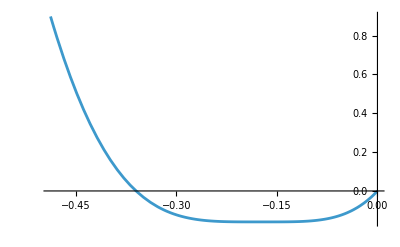

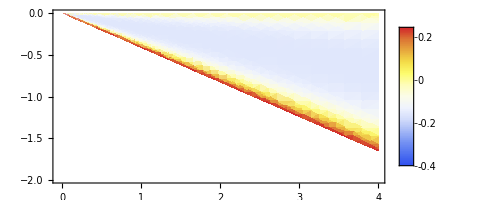

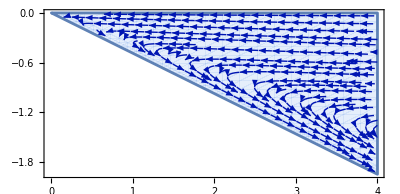

```mathematica
toplotxc=ReplaceAll[vx,{Subscript[A, 3]->A,Subscript[B, 3]->B,Subscript[c, 3]->c,Subscript[d, 3]->d}];
toplotzc=ReplaceAll[vz,{Subscript[A, 3]->A,Subscript[B, 3]->B,Subscript[c, 3]->c,Subscript[d, 3]->d}];
Rotate[Plot[ReplaceAll[toplotxc,{x->1}],{z,-Tan[δval],0},PlotRange->Full],Pi/2]

DensityPlot[toplotxc,{x,-0.04,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},0>=Tan[z/x]>=-δval],AspectRatio->Automatic]

p1=StreamPlot[{toplotxc,toplotzc},{x,-0.01,4},{z,-4*Tan[δval],0},RegionFunction->Function[{x,z},z+Tan[δval]*x>=0 && x>=0.0],StreamPoints->Fine,StreamScale->Tiny,AspectRatio->Automatic]
```

# Insert boundary conditions for oceanic mantle

```mathematica
eq1 = ReplaceAll[vx,{ArcTan[x,z]->-π,z->0,x->-1}];
eq2 = ReplaceAll[vz,{ArcTan[x,z]->-π,z->0,x->-1}];
eq3=ReplaceAll[vx,{ArcTan[x,z]->-δ,z->-Tan[δ],x->1}]//FullSimplify;
eq4=ReplaceAll[vz,{ArcTan[x,z]->-δ,z->-Tan[δ],x->1}]//FullSimplify;
(*Substitute the numerical delta equations*)
eqsNumerical={eq1==1,eq2==0,eq3==Cos[δval],eq4==-Sin[δval]}/.{δ->δval};
(*Numerical Solver*)
numSol=FindRoot[eqsNumerical,{{Subscript[A, 3],1.0},{Subscript[B, 3],1.0},{Subscript[c, 3],1.0},{Subscript[d, 3],0.1}}]
(*Extract the values*)
{A,B,c,d}={Subscript[A, 3],Subscript[B, 3],Subscript[c, 3],Subscript[d, 3]}/. numSol;
```

{2451.49_3→-1.32859,425.254_3→-0.30673,111.264_3→0.0197374,-82.0186_3→-2.4172}

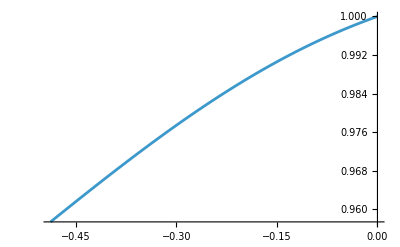

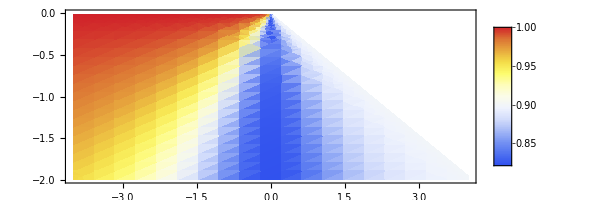

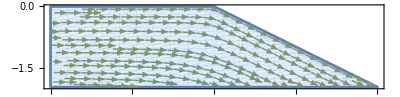

```mathematica
toplotxo=ReplaceAll[vx,{Subscript[A, 3]->A,Subscript[B, 3]->B,Subscript[c, 3]->c,Subscript[d, 3]->d}];
toplotzo=ReplaceAll[vz,{Subscript[A, 3]->A,Subscript[B, 3]->B,Subscript[c, 3]->c,Subscript[d, 3]->d}];
Rotate[Plot[ReplaceAll[toplotxo,{x->-1}],{z,-Tan[δval],0}],Pi/2]

DensityPlot[toplotxo,{x,-4,4},{z,-2,0},PlotLegends->Automatic,PlotPoints->20,ColorFunction->"TemperatureMap",RegionFunction->Function[{x,z},z+Tan[δval]*x<=0],AspectRatio->Automatic]

p2=StreamPlot[{toplotxo,toplotzo},{x,-4,4},{z,-4*Tan[δval],0},StreamPoints->Fine,StreamScale->Tiny,AspectRatio->Automatic,RegionFunction->Function[{x,z},z+Tan[δval]*x<=0 ],StreamColorFunction->"ArmyColors"]
```